# Lz4 LG model from integration of Fθ - THESE

```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True]
ClearAll["Global`*"]
Needs["NumericalCalculus`"]
$Assumptions={_∈Reals,-Pi<θ<Pi &&-Pi<ϕ<Pi && -Pi<φ<Pi && -Pi<δ<Pi && c > 0 && ω >0 && w0>0 && z >0 && h >0 && E0 > 0 && r >0 && l∈Reals && x∈Reals && y ∈Reals &&t>0 && β∈Reals && α∈Reals && γ∈Reals}
rule2carte ={r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
rule2pol = {x->r Cos[θ],y-> r Sin[θ]};
k := ω/c
zR:=1/2*k*w0^2 (*Rayleigh range*)
w[z] := w0 *Sqrt[1+(z/zR)^2] (* Beam radius *)
R[z] := z*(1+(zR/z)^2) (* Radius of curvature *)
p:=0
n := Abs[l]+2*p
G[z]:= (n+1)ArcTan[z/zR](* Gouy phase at z *)
Gpl := Sqrt[(2*Factorial[p])/(Pi*Factorial[p+Abs[l]])]*0+1
Lp := 1(* generalized Laguerre polynomials p = 0 -> Lp = 1 *)
If[p ==1,Lp = 1 +Abs[l]-(2*r^2)/w[z]^2]
f[r]=(w0*Gpl)/w[z]((r √2)/w[z])^Abs[l]*Exp[-r^2/w[z]^2]
u[r,θ,z]:=Evaluate[f[r]*Lp*Exp[-I k r^2/(2 R[z])]*Exp[-I*l*θ]*Exp[I*G[z]]](*((2r^2)/w[z]^2)*)
tempEnv = Exp[-(t-z)^2/Tp^2]

Ex[r,θ,z]=E0*u[r,θ,z]*Exp[-I*k*z+I*ω*t]; (**tempEnv*)
Ey[r,θ,z]=0;
Ez[r,θ,z]=0;

Ex[x,y,z] =Ex[r,θ,z]/. {r->Norm[{x,y}],θ->ArcTan[x,y]};

Clear[l]
l=1;
c = 1;
ω = 1;
φ=0;
Ev = Evaluate[{Ex[x,y,z],0,0}]/.{Abs[x]->RealAbs[x],Abs[y]->RealAbs[y]}//Simplify
```

{_∈ℝ,-π<θ<π&&-π<ϕ<π&&-π<φ<π&&-π<δ<π&&c>0&&ω>0&&w0>0&&z>0&&h>0&&E0>0&&r>0&&l∈ℝ&&x∈ℝ&&y∈ℝ&&t>0&&β∈ℝ&&α∈ℝ&&γ∈ℝ}

(2^(Abs[l]/2) ⅇ^(-r^2/(w0^2 (1+(4 c^2 z^2)/(w0^4 ω^2)))) (r/(w0 √(1+(4 c^2 z^2)/(w0^4 ω^2))))^Abs[l])/(√(1+(4 c^2 z^2)/(w0^4 ω^2)))

ⅇ^(-(t-z)^2/Tp^2)

{(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 √(x^2+y^2))/(w0^4+4 z^2),0,0}

```mathematica
B =-Integrate[Ev{x,y,z},t]//Simplify
divB :=B{x,y,z} /.{x ->α* w0,z-> γ* zR ,y->β*w0,w0->h};
SF = FullSimplify[Normal[Series[divB,{h,∞,12}]]];
Print["Div B O1 :",SF];
Evn = Integrate[B{x,y,z},t]//Simplify;
divE =Evn {x,y,z}/.{x ->α* w0 ,z-> γ* zR, y->β*w0};
S = Simplify[Normal[Series[divE,{h,∞,12}]]];
Print["Div E O1 :",S]
```

{0,(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 √(x^2+y^2) (w0^4+w0^2 (-4-4 ⅈ z)+2 (x^2+y^2-2 z (-2 ⅈ+z))))/((w0^2-2 ⅈ z)^3 (w0^2+2 ⅈ z)),(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 (x+ⅈ y) (-w0^2+2 ⅈ x y+2 y^2+2 ⅈ z))/(√(x^2+y^2) (w0^2-2 ⅈ z)^2 (w0^2+2 ⅈ z))}

Div B O1 :0

Div E O1 :0

## Ez LG

```mathematica
EzCP=-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](-2*I*E0* α *ω*Exp[-(ⅈ (α^2+β^2-ⅈ φ-γ φ-ⅈ t ω-t γ ω-ⅈ ArcTan[γ]-γ ArcTan[γ]))/(ⅈ+γ)])/(c h (ⅈ+γ) √(1+γ^2))/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}
EzO3=Evaluate[-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](√2 ⅇ^(-1/2 ⅈ ((2 α^2)/(ⅈ+γ)+(2 β^2)/(ⅈ+γ)-2 (φ+t ω)-4 ArcTan[γ])) E0 (ⅈ-2 ⅈ α^2-2 α β+γ) ω)/(c h (-ⅈ+γ) (ⅈ+γ)^2)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}]; (*L=1*)
EzO5=-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](-2 ⅈ √2 ⅇ^(-(ⅈ (2 α^2+2 β^2+(ⅈ+γ) (-2 (φ+t ω))))/(2 (ⅈ+γ))) E0 (-2 α^4+2 ⅈ α^3 β+2 ⅈ α β (-3+β^2+3 ⅈ γ)+α^2 (7-2 β^2-7 ⅈ γ)+(ⅈ+γ) (2 ⅈ-ⅈ β^2+2 γ)) ω)/(c h^3 (ⅈ+γ)^5)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}(*L=l*);
EzLGO3 = EzO3 
EzLGO5 = EzO3 +EzO5

BzLG = (√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 (x+ⅈ y) (-w0^2+2 ⅈ x y+2 y^2+2 ⅈ z))/(√(x^2+y^2) (w0^2-2 ⅈ z)^2 (w0^2+2 ⅈ z))
```

-(2 ⅇ^(-ⅈ z-(ⅈ (-ⅈ t+x^2/w0^2+y^2/w0^2-(2 t z)/w0^2-ⅈ ArcTan[(2 z)/w0^2]-(2 z ArcTan[(2 z)/w0^2])/w0^2))/(ⅈ+(2 z)/w0^2)) E0 x)/(w0^2 (ⅈ+(2 z)/w0^2) √(1+(4 z^2)/w0^4))

-(ⅈ √2 ⅇ^(-ⅈ z-1/2 ⅈ (-2 t+(2 x^2)/(w0^2 (ⅈ+(2 z)/w0^2))+(2 y^2)/(w0^2 (ⅈ+(2 z)/w0^2))-4 ArcTan[(2 z)/w0^2])) E0 (ⅈ-(2 ⅈ x^2)/w0^2-(2 x y)/w0^2+(2 z)/w0^2))/(w0 (-ⅈ+(2 z)/w0^2) (ⅈ+(2 z)/w0^2)^2)

-(ⅈ √2 ⅇ^(-ⅈ z-1/2 ⅈ (-2 t+(2 x^2)/(w0^2 (ⅈ+(2 z)/w0^2))+(2 y^2)/(w0^2 (ⅈ+(2 z)/w0^2))-4 ArcTan[(2 z)/w0^2])) E0 (ⅈ-(2 ⅈ x^2)/w0^2-(2 x y)/w0^2+(2 z)/w0^2))/(w0 (-ⅈ+(2 z)/w0^2) (ⅈ+(2 z)/w0^2)^2)-(2 √2 ⅇ^(-ⅈ z-(ⅈ ((2 x^2)/w0^2+(2 y^2)/w0^2-2 t (ⅈ+(2 z)/w0^2)))/(2 (ⅈ+(2 z)/w0^2))) E0 (-(2 x^4)/w0^4+(2 ⅈ x^3 y)/w0^4+(2 ⅈ x y (-3+y^2/w0^2+(6 ⅈ z)/w0^2))/w0^2+(x^2 (7-(2 y^2)/w0^2-(14 ⅈ z)/w0^2))/w0^2+(ⅈ+(2 z)/w0^2) (2 ⅈ-(ⅈ y^2)/w0^2+(4 z)/w0^2)))/(w0^3 (ⅈ+(2 z)/w0^2)^5)

(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 (x+ⅈ y) (-w0^2+2 ⅈ x y+2 y^2+2 ⅈ z))/(√(x^2+y^2) (w0^2-2 ⅈ z)^2 (w0^2+2 ⅈ z))

## To Python

```mathematica
EvnO3={Ex[x,y,z],0,EzLG03}
EvnO5={Ex[x,y,z],0,EzLG05}
B =-Integrate[EvnO3{x,y,z},t]//Simplify
IntEzLGO3[r_,θ_,z_] = (ComplexExpand[EzLGO3*Conjugate[EzLGO3]]//Simplify)/.rule2pol//Simplify;
IntEzLGO5[r_,θ_,z_] = (ComplexExpand[EzLGO5*Conjugate[EzLGO5]]//Simplify)/.rule2pol//Simplify;
FθLG03[r_,θ_,z_] = -1/4*1/r*D[IntEzLGO3[r,θ,z],θ]//Simplify
FθLG05[r_,θ_,z_] = -1/4*1/r*D[IntEzLGO5[r,θ,z],θ]//FullSimplify
```

{(√2 ⅇ^(ⅈ t-ⅈ z-(ⅈ (Abs[x]^2+Abs[y]^2))/(2 (1+w0^4/(4 z^2)) z)-(Abs[x]^2+Abs[y]^2)/(w0^2 (1+(4 z^2)/w0^4))+2 ⅈ ArcTan[(2 z)/w0^2]-ⅈ ArcTan[x,y]) E0 √(Abs[x]^2+Abs[y]^2))/(w0 (1+(4 z^2)/w0^4)),0,EzLG03}

{(√2 ⅇ^(ⅈ t-ⅈ z-(ⅈ (Abs[x]^2+Abs[y]^2))/(2 (1+w0^4/(4 z^2)) z)-(Abs[x]^2+Abs[y]^2)/(w0^2 (1+(4 z^2)/w0^4))+2 ⅈ ArcTan[(2 z)/w0^2]-ⅈ ArcTan[x,y]) E0 √(Abs[x]^2+Abs[y]^2))/(w0 (1+(4 z^2)/w0^4)),0,EzLG05}

{0,(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 √(x^2+y^2) (w0^4+w0^2 (-4-4 ⅈ z)+2 (x^2+y^2-2 z (-2 ⅈ+z))))/((w0^2-2 ⅈ z)^3 (w0^2+2 ⅈ z)),(ⅈ √2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 (x (ⅈ w0^2+2 z)+(-w0^2+2 (x^2+y^2+ⅈ z)) Abs[y] Abs'[y]))/(√(x^2+y^2) (w0^2-2 ⅈ z)^2 (w0^2+2 ⅈ z))}

(2 ⅇ^(-(2 r^2 w0^2)/(w0^4+4 z^2)) E0^2 r w0^6 (2 z Cos[2 θ]+(r^2-w0^2) Sin[2 θ]))/((w0^4+4 z^2)^3)

1/((w0^4+4 z^2)^5)2 ⅇ^(-(2 r^2 w0^2)/(w0^4+4 z^2)) E0^2 r w0^6 (2 z (4 r^4-4 r^2 (4 w0^2+w0^4-4 z^2)+(w0^4+4 z^2) (24+12 w0^2+w0^4+4 z^2)) Cos[2 θ]+(4 r^6-4 r^4 (7 w0^2+w0^4-4 z^2)-(w0^4+4 z^2) (w0^2 (4+w0^2) (6+w0^2)+4 (-2+w0^2) z^2)+r^2 (w0^4 (56+16 w0^2+w0^4)+8 (20+4 w0^2+w0^4) z^2+16 z^4)) Sin[2 θ])

```mathematica
l0=2*Pi
E0=2.0
w0=2.5*l0
FθLG03[1,2,3]
FθLG05[1,2,3]
```

2 π

2.

15.708

0.000096003

0.0000999024

```mathematica
D[Exp[-((t-Tp))^2]]
```

## Intensity and Lz2

```mathematica
IntEzLGO3[r_,θ_,z_] = (ComplexExpand[EzLGO3*Conjugate[EzLGO3]]//Simplify)*Sin[Pi*(t)/Tp]^(4*1)/.rule2pol//Simplify;
IntEzLGO5[r_,θ_,z_] = (ComplexExpand[EzLGO5*Conjugate[EzLGO5]]//Simplify)*Sin[Pi*(t)/Tp]^(4*1)/.rule2pol//Simplify;
IntBzLGCart[x_,y_,z_] = (ComplexExpand[BzLG*Conjugate[BzLG]]//Simplify)*Sin[Pi*(t)/Tp]^(4*1)//Simplify;
IntBzLG[r_,θ_,z_]=IntBzLGCart[x,y,z]/.rule2pol;

f0[r_]=(w0*Gpl)/w0((r √2)/w0)^Abs[l]*Exp[-r^2/w0^2];

Fθ[r_,θ_,z_,t_] = -1/4*1/r*D[IntEzLGO5[r,θ,z],θ]//Simplify;
vs[a_]=1-Sqrt[(2-a^2)/2];
zModel[z_] = z(*+0.25*t*);
θModel[θ_] = θ + Fθ[r,θ,z,t]*t^2/2;
rModel[r_,z_,t_]= r+-E0^2/4*D[f[r]^2,r]*t^2/2;

Lz2Int[r_,θ_,z_] = r*Integrate[Fθ[r,θ,z,t],{t,0,Tp}]//FullSimplify
Lz2[r_,θ_,z_] = r*Fθ[r,θ,z,Tp/2]*3/8*Tp//FullSimplify
(*Lz2Cart[x_,y_,z_] =r*Integrate[Fθ[r,θ,z,t],{t,0,Tp}]//Simplify/.rule2carte//Simplify;*)
```

$Aborted

$Aborted

$Aborted

r ∫_0^Tp Fθ[r,θ,z,t]ⅆt

3/8 r Tp Fθ[r,θ,z,Tp/2]

```mathematica
FθTime[r_,θ_,z_,t_] =Fθ[r,θModel[θ],z,t];
Lz4[r_,θ_,z_]:=r*NIntegrate[FθTime[r,θ,z,t],{t,0,Tp}]
(*FθTimeCart[x_,y_,z_,t_] =FθTime[Sqrt[x^2+y^2],ArcTan[x,y],z,t]//Simplify*)

(*Lz4R[ri_,θi_,zi_]:=NIntegrate[rModel*FθTime[ri,θi,zi,t],{t,0,Tp}]
Lz4Cart[x_,y_,z_]:=(Sqrt[x^2+y^2]*NIntegrate[FθTimeCart[x,y,z,t],{t,0,Tp}])*)
```

```mathematica
(*Integrate[FθTime,{t,0,Tp}]*)
```

```mathematica
(*Lz4[r_,θ_,z_] = r*Integrate[Fθ[r,θModel,zModel],{t,0,Tp}]*)
```

```mathematica
dr[r_,t_]=1*(3/8)*-E0^2/4*f0[r]^2/r*(Abs[l]-2*(r/w0)^2)*t^2/2;
Lz4R[r_,θ_,z_]:=NIntegrate[(rModel[r,z,t])*FθTime[rModel[r,z,t],θ,z,t],{t,0,Tp}]
Lz4R2[r_,θ_,z_]:=NIntegrate[(r+dr[r,t])*FθTime[r+dr[r,t],θ,z,t],{t,0,Tp}]
(*Lz4RCart[ri_,θi_,zi_]:=NIntegrate[(ri+dr[ri,t])*FθTime[ri+dr[ri,t],θi,zi,t],{t,0,Tp}]*)
```

# Numerical

```mathematica
rModel[1,2,2]
```

0.968116

```mathematica
(rModel[1,0,5])*FθTime[rModel[1,0,5],1,0,5]//Simplify
```

-2.1222×10^-6

```mathematica
NIntegrate[(rModel[1,z,t])*FθTime[rModel[1,t],1,0,t],{t,0,Tp}]
```

NIntegrate::inumr: The integrand -2.36011×10^-21 ⅇ^(-0.00810569 rModel[1,t]^2) rModel[1,t]^2 Sin[0.0833333 t]^4 (0.+2. (1.12826×10^15-7.31625×10^12 rModel[1,t]^2+7.41291×10^9 rModel[1,t]^4) Sin[2 (1-1.18005×10^-21 Power[«2»] Power[«2»] rModel[«2»] Plus[«3»] Power[«2»])]+60880.7 (9.14892×10^11-3.70987×10^9 rModel[1,t]^2+6908.72 rModel[1,t]^4-4 rModel[1,t]^6) Sin[2 (1-1.18005×10^-21 Power[«2»] Power[«2»] rModel[«2»] Plus[«3»] Power[«2»])]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,37.6991}}.

NIntegrate[rModel[1,t] FθTime[rModel[1,t],1,0,t],{t,0,Tp}]

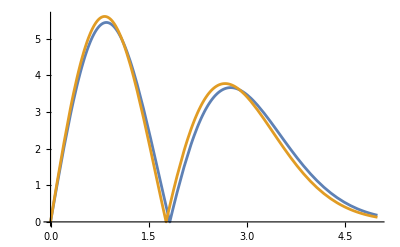

```mathematica
Plot[{Abs[(rModel[r*l0,5*l0,Tp]-r*l0)/l0],5*Abs[(dr[r*l0,Tp])/l0]},{r,0,2*w0/l0}]
```

```mathematica
FθTime[1,2,3,4]
```

```mathematica
E0=2;
c = 1;
ω =1;
k = ω/c;
l0 = N[2*Pi];
Nw0 =2.5;
w0 = Nw0*l0;
z0=5*l0
Tp =6*l0;
h =N[ ω*w0/c];
Print["w0 = ",w0]
φ = 0;
l=1;
```

31.4159

w0 = 15.708

```mathematica
Lz4R[1,0,2]
```

7.80458×10^-8

```mathematica
Lz2[1,2,3]
Lz4[1,2,3]
Lz4R[1,2,3]
```

0.00141234

0.00144636

0.00717715

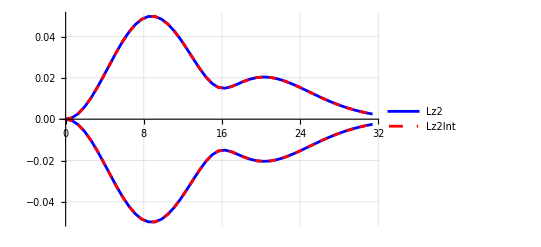

```mathematica
Plot[{FindMaximum[Lz2[r,theta,z0],{theta,0,2Pi}][[1]],FindMinimum[Lz2[r,theta,z0],{theta,0,2Pi}][[1]],
FindMaximum[Lz2Int[r,theta,z0],{theta,0,2Pi}][[1]],FindMinimum[Lz2Int[r,theta,z0],{theta,0,2Pi}][[1]]},{r,0.001,2*w0},PlotStyle->{Blue,Blue,{Red,Dashed},{Red,Dashed},Green,Green,Orange,Orange},PlotLegends->Placed[{"Lz2",None,"Lz2Int",None,"Lz4",None,"Lz4R2",None},Right],GridLines->Automatic,PlotPoints->25,MaxRecursion->1]
```

```mathematica
Lz2
```

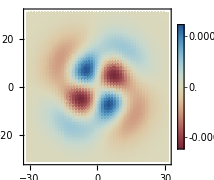

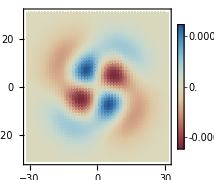

```mathematica
DensityPlot[Lz2[Sqrt[x^2+y^2],ArcTan[y,x],z0],
{x,-2*w0,2*w0},{y,-2*w0,2*w0},PlotPoints->{50,50},PlotLegends->Automatic,ImageSize->Small,ColorFunction->"RedBlueTones",PlotRange->All]
DensityPlot[Lz4[Sqrt[x^2+y^2],ArcTan[y,x],z0],
{x,-2*w0,2*w0},{y,-2*w0,2*w0},PlotPoints->{50,50},PlotLegends->Automatic,ImageSize->Small,ColorFunction->"RedBlueTones",PlotRange->All]
```

```mathematica
Manipulate[DensityPlot[Lz2Cart[x,y,z],
{x,-2*w0,2*w0},{y,-2*w0,2*w0},PlotPoints->{50,50},PlotLegends->Automatic,ImageSize->Small,ColorFunction->"RedBlueTones",PlotRange->All],{z,0,6*l0}]
```

DensityPlot::plln: Limiting value -2 w0 in {x,-2 w0,2 w0} is not a machine-sized real number.

```mathematica
FθTime[2,Pi/4,0]
```

FθTime[2,π/4,0]

```mathematica
FindMinimum[Lz4R[1,θ,0.001],θ]
FindMaximum[Lz4R[1,θ,0.001],θ]
```

NIntegrate::inumr: The integrand -(1.43535×10^7 «3» (8. t (-2.31938×10^16+2.87069×10^9 t^2+710.612 t^4+(1+Times[«2»])^2 (4.07989×10^12-3.02981×10^6 Power[«2»]+0.0625 Power[«2»])) Cos[2 (θ-9.9016×10^-9 Power[«2»] Power[«2»] Plus[«2»] Cos[«1»] Power[«2»] Sin[«1»]+8.53816×10^-25 Power[«2»] Power[«2»] Plus[«2»] Plus[«4»] Power[«2»] Sin[«1»])]+«1»+(2.01987×10^6+0.25 t^2) (t («1») Cos[2 Plus[«3»]]+«1»+(«1») Sin[2 Plus[«1»]])))/((2.01987×10^6+0.25 t^2)^6) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,125.664}}.

NIntegrate::inumr: The integrand -(1.43535×10^7 «3» (8. t (-2.31938×10^16+2.87069×10^9 t^2+710.612 t^4+(1.+Times[«2»])^2 (4.07989×10^12-3.02981×10^6 Power[«2»]+0.0625 Power[«2»])) Cos[2 (θ-9.9016×10^-9 Power[«2»] Power[«2»] Plus[«2»] Cos[«1»] Power[«2»] Sin[«1»]+8.53816×10^-25 Power[«2»] Power[«2»] Plus[«2»] Plus[«4»] Power[«2»] Sin[«1»])]+«1»+(2.01987×10^6+0.25 t^2) (t («1») Cos[2 Plus[«3»]]+«1»+(«1») Sin[2 «1»])))/((2.01987×10^6+0.25 t^2)^6) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,125.664}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{-4.65648×10^-7,{θ→0.796506}}

NIntegrate::inumr: The integrand -(1.43535×10^7 «3» (8. t (-2.31938×10^16+2.87069×10^9 t^2+710.612 t^4+(1+Times[«2»])^2 (4.07989×10^12-3.02981×10^6 Power[«2»]+0.0625 Power[«2»])) Cos[2 (θ-9.9016×10^-9 Power[«2»] Power[«2»] Plus[«2»] Cos[«1»] Power[«2»] Sin[«1»]+8.53816×10^-25 Power[«2»] Power[«2»] Plus[«2»] Plus[«4»] Power[«2»] Sin[«1»])]+«1»+(2.01987×10^6+0.25 t^2) (t («1») Cos[2 Plus[«3»]]+«1»+(«1») Sin[2 Plus[«1»]])))/((2.01987×10^6+0.25 t^2)^6) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,125.664}}.

NIntegrate::inumr: The integrand -(1.43535×10^7 «3» (8. t (-2.31938×10^16+2.87069×10^9 t^2+710.612 t^4+(1.+Times[«2»])^2 (4.07989×10^12-3.02981×10^6 Power[«2»]+0.0625 Power[«2»])) Cos[2 (θ-9.9016×10^-9 Power[«2»] Power[«2»] Plus[«2»] Cos[«1»] Power[«2»] Sin[«1»]+8.53816×10^-25 Power[«2»] Power[«2»] Plus[«2»] Plus[«4»] Power[«2»] Sin[«1»])]+«1»+(2.01987×10^6+0.25 t^2) (t («1») Cos[2 Plus[«3»]]+«1»+(«1») Sin[2 «1»])))/((2.01987×10^6+0.25 t^2)^6) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,125.664}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{4.65648×10^-7,{θ→2.36727}}

```mathematica
ListDensityPlot[Lz4table,PlotRange->All,PlotLegends->Automatic,ColorFunction->"RedBlueTones",ImageSize->Small,PlotLabel->"IntEz LG Z"]
```

ListDensityPlot::arrayerr: Lz4table must be a valid array.

ListDensityPlot[Lz4table,PlotRange→All,PlotLegends→Automatic,ColorFunction→RedBlueTones,ImageSize→Small,PlotLabel→IntEz LG Z]